Background

```mathematica
coord ={t,r,θ1,θ2,θ3};
metric=({{-Λ/(6 r^2)(r^2-re^2)(rc^2-r^2), 0, 0, 0, 0}, {0, 1/(Λ/(6 r^2)(r^2-re^2)(rc^2-r^2)), 0, 0, 0}, {0, 0, r^2, 0, 0}, {0, 0, 0, r^2 Sin[θ1]^2, 0}, {0, 0, 0, 0, r^2 Sin[θ1]^2 Sin[θ2]^2}});
```

```mathematica
$Assumptions= And[t∈Reals,ω>0,ϵ>0,r>1,r<Sqrt[5],l>0,x>0,A2∈Reals,A1∈Reals,A0∈Reals];
metricsign=-1;
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<diffgeo.m
```

```mathematica
EEstep1 = RicciTensor-1/2 RicciScalar*metric  + Λ* metric;
```

```mathematica
EEstep2 = EEstep1  /.re->((3-Sqrt[9-12MΛ])/Λ)^(1/2)/.rc->((3+Sqrt[9-12MΛ])/Λ)^(1/2)//FullSimplify
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
Riemann;
```

```mathematica
contract[lower[Riemann,{4}]**lower[Riemann,{4}],{1,5},{2,6},{3,7},{4,8}]/.re->((3-Sqrt[9-12MΛ])/Λ)^(1/2)/.rc->((3+Sqrt[9-12MΛ])/Λ)^(1/2)//FullSimplify
```

(288 MΛ^2)/(r^8 Λ^2)+(10 Λ^2)/9

Perturbation

```mathematica
Φ=Exp[-ⅈ*ω*t]*Ψ[r];
```

```mathematica
SEstep1=scalarLaplacian[Φ] //Simplify;
SEstep2=Collect[(SEstep1/Exp[-ⅈ*ω*t]-(l(l+2))/r^2 Ψ[r]),{Ψ''[r],Ψ'[r],Ψ[r]},Simplify]
```

(-(l (2+l))/r^2-(6 r^2 ω^2)/((r^2-rc^2) (r^2-re^2) Λ)) Ψ[r]-((5 r^4+rc^2 re^2-3 r^2 (rc^2+re^2)) Λ Ψ'[r])/(6 r^3)-((r^2-rc^2) (r^2-re^2) Λ Ψ''[r])/(6 r^2)

```mathematica
c[r_]=(-(l (2+l))/r^2-(6 r^2 ω^2)/((r^2-rc^2) (r^2-re^2) Λ))//FullSimplify;
b[r_]=-((5 r^4+rc^2 re^2-3 r^2 (rc^2+re^2)) Λ)/(6 r^3)//FullSimplify;
a[r_]=-((r^2-rc^2) (r^2-re^2) Λ)/(6 r^2)//FullSimplify;
```

```mathematica
V0[r_]=-1/(4 a[r]^2)(2b[r]*a'[r]-b[r]^2-2a[r]*(b'[r]-2c[r]));
DetermiV0[r_]=Collect[(4 r^2 (r^2-rc^2)^2 (r^2-re^2)^2 Λ^2)V0[r]//FullSimplify,r] 
V[r_]=-1/(4 a[r]^2)(2b[r]*a'[r]-b[r]^2-2a[r]*(b'[r]-2c[r]))/.re->Sqrt[1]/.rc->Sqrt[5]/.Λ->1//FullSimplify
```

15 r^8 Λ^2-rc^4 re^4 Λ^2+r^2 (-48 l rc^2 re^2 Λ-24 l^2 rc^2 re^2 Λ-6 rc^2 re^2 (rc^2+re^2) Λ^2)+r^4 (48 l rc^2 Λ+24 l^2 rc^2 Λ+48 l re^2 Λ+24 l^2 re^2 Λ+3 (rc^4+12 rc^2 re^2+re^4) Λ^2)+r^6 (-48 l Λ-24 l^2 Λ-22 (rc^2+re^2) Λ^2-144 ω^2)

(-25-60 (3+2 l (2+l)) r^2+6 (43+24 l (2+l)) r^4+15 r^8-12 r^6 (11+2 l (2+l)+12 ω^2))/(4 r^2 (5-6 r^2+r^4)^2)

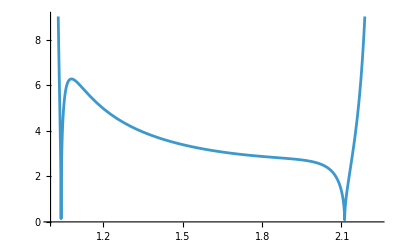

```mathematica
Plot[Sqrt[Abs[V[r]]]/.ω->0.1/.l->2,{r,Sqrt[1],Sqrt[5]}]
```

```mathematica
Vevent0[ϵ_]=Collect[Normal[Series[V0[r],{r,re,0}]]/.r->re+ϵ/.re->((3-Sqrt[9-12MΛ])/Λ)^(1/2)/.rc->((3+Sqrt[9-12MΛ])/Λ)^(1/2)//FullSimplify,ϵ];
Vcosmo0[ϵ_]=Collect[Normal[Series[V0[r],{r,rc,0}]]/.r->rc-ϵ/.re->((3-Sqrt[9-12MΛ])/Λ)^(1/2)/.rc->((3+Sqrt[9-12MΛ])/Λ)^(1/2)//FullSimplify,ϵ];
NoPoleV[r_]=(r-Sqrt[5])^2(r-1)^2 V[r]//FullSimplify;
Vcosmo[r_]=Normal[Series[V[r],{r,Sqrt[5],0}]]
Vevent[r_]=Normal[Series[V[r],{r,1,0}]]
```

(-4-45 ω^2)/(16 (-√5+r)^2)+1/20 (-4+18 l+9 l^2-45 ω^2)+(16-12 l-6 l^2+45 ω^2)/(8 √5 (-√5+r))

(-4-9 ω^2)/(16 (-1+r)^2)+(2+6 l+3 l^2-9 ω^2)/(4 (-1+r))-7/16 (4+9 ω^2)

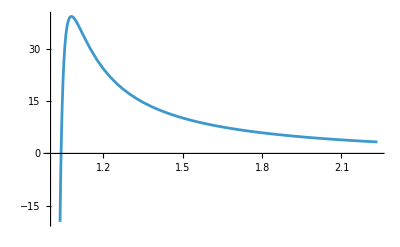

```mathematica
Plot[VeventNoPole[r]/.ω->0.1/.l->2,{r,1,Sqrt[5]}]
```

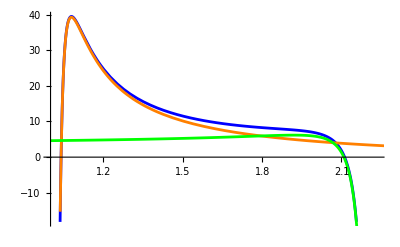

```mathematica
Show[Plot[V[r]/.ω->0.1/.l->2,{r,1,Sqrt[5]},PlotStyle->{Blue}],
Plot[Vevent[r]/.ω->0.1/.l->2,{r,1,2.9},PlotStyle->{Orange}],
Plot[Vcosmo[r]/.ω->0.1/.l->2,{r,1,2.9},PlotStyle->{Green}]]
```

```mathematica
Hey[ϵ_]=Integrate[Sqrt[a+b/ϵ+c/ϵ^2],ϵ]//FullSimplify
```

√(c+ϵ (b+a ϵ))+2 √c ArcTanh[(√a ϵ-√(c+ϵ (b+a ϵ)))/(√c)]-(b Log[b+2 a ϵ-2 √a √(c+ϵ (b+a ϵ))])/(2 √a)

```mathematica
Inside0[r_]=1/(rc-re)^5(c0 (r-re)^3 (6 r^2+10 rc^2-5 rc re+re^2+3 r (-5 rc+re))-(r-rc) (e0 (r-rc)^2 (6 r^2+3 r rc+rc^2-5 (3 r+rc) re+10 re^2)+(r-re) (rc-re) (c1 (r-re)^2 (3 r-4 rc+re)-(r-rc) (-e1 (r-rc) (3 r+rc-4 re)+(r-re) (rc-re) (c2 r-e2 r+e2 rc-c2 re)))))
```

(c0 (r-re)^3 (6 r^2+10 rc^2-5 rc re+re^2+3 r (-5 rc+re))-(r-rc) (e0 (r-rc)^2 (6 r^2+3 r rc+rc^2-5 (3 r+rc) re+10 re^2)+(r-re) (rc-re) (c1 (r-re)^2 (3 r-4 rc+re)-(r-rc) (-e1 (r-rc) (3 r+rc-4 re)+(r-re) (rc-re) (c2 r-e2 r+e2 rc-c2 re)))))/(rc-re)^5

```mathematica
Inside1[r_]=1/((r-rc)^2 (r-re)^2 (rc-re)^5)(c0 (r-re)^3 (6 r^2+10 rc^2-5 rc re+re^2+3 r (-5 rc+re))-(r-rc) (e0 (r-rc)^2 (6 r^2+3 r rc+rc^2-5 (3 r+rc) re+10 re^2)+(r-re) (rc-re) (c1 (r-re)^2 (3 r-4 rc+re)-(r-rc) (-e1 (r-rc) (3 r+rc-4 re)+(r-re) (rc-re) (c2 r-e2 r+e2 rc-c2 re)))))/.e0->-1/16 (-1+√5)^2 (4+9 ω^2)/.e1->1/8  (20-4 √5+72 l-24 √5 l+36 l^2-12 √5 l^2-117 ω^2+45 √5 ω^2)/.e2->1/16 (-156+40 √5+48 l-48 √5 l+24 l^2-24 √5 l^2-459 ω^2+198 √5 ω^2)/.c0->-1/16 (-1+√5)^2 (4+45 ω^2)/.c1->-1/40 (-1+√5)(-60+16 √5+60 l-12 √5 l+30 l^2-6 √5 l^2+45 √5 ω^2)/.c2->1/80 (204-32 √5+192 l-96 √5 l+96 l^2-48 √5 l^2-405 ω^2+180 √5 ω^2)/.rc->Sqrt[5]/.re->1//FullSimplify
```

1/(40 (-1+√5)^4 (√5-r)^2 (-1+r)^2)(20 (-1239+529 √5)+96 l (-1+r) (110-45 √5+r (225-106 √5+r (69-28 √5+r (-33+14 √5+(-11+5 √5) r))))+48 l^2 (-1+r) (110-45 √5+r (225-106 √5+r (69-28 √5+r (-33+14 √5+(-11+5 √5) r))))+675 (-47+21 √5) ω^2+r (14840-5368 √5-900 (-65+29 √5) ω^2+r (12712-6936 √5+90 (-81+35 √5) ω^2+r (64 (-44+29 √5)+900 (-29+13 √5) ω^2+r (-4764+1988 √5+8 (-119+55 √5) r+135 (-47+21 √5) ω^2)))))

```mathematica
f[r_]=Integrate[Sqrt[-((-4-9 ω^2)/(16 (r-1)^2)+(2+6 l+3 l^2-9 ω^2)/(4 (r-1))-7/16 (4+9 ω^2))],r]//FullSimplify
```

1/4 √(4 (10+3 l (2+l)-16 r-3 l (2+l) r+7 r^2)+9 (4+r (-10+7 r)) ω^2)+(-7 (4+9 ω^2) ArcTanh[(8-6 l (2+l) (-1+r)-4 r-9 ω^2+18 r ω^2)/(√((4+9 ω^2) (4 (10+3 l (2+l)-16 r-3 l (2+l) r+7 r^2)+9 (4+r (-10+7 r)) ω^2)))]-2 √7 (2+3 l (2+l)-9 ω^2) ArcTanh[(-32-6 l (2+l)+28 r+9 (-5+7 r) ω^2)/(√7 √((4+9 ω^2) (4 (10+3 l (2+l)-16 r-3 l (2+l) r+7 r^2)+9 (4+r (-10+7 r)) ω^2)))])/(28 √(4+9 ω^2))

```mathematica
-f[1.000001]+f[1.0399033]/.l->2/.ω->0.1
```

5.04421+0. ⅈ

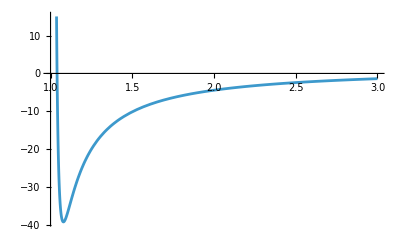

```mathematica
Plot[-((-4-9 ω^2)/(16 (r-1)^2)+(2+6 l+3 l^2-9 ω^2)/(4 (r-1))-7/16 (4+9 ω^2))/.l->2/.ω->0.1,{r,1,3}]
```

```mathematica
f[1.000001]/.l->2/.ω->0.1//FullSimplify
```

-5.04422-3.00899 ⅈ

```mathematica
fn[x_]=NIntegrate[Sqrt[-((-4-9 ω^2)/(16 (r-1)^2)+(2+6 l+3 l^2-9 ω^2)/(4 (r-1))-7/16 (4+9 ω^2))/.l->2/.ω->0.1],{r,1.000001}]
```

NIntegrate[√(-((-4-9 ω^2)/(16 (r-1)^2)+(2+6 l+3 l^2-9 ω^2)/(4 (r-1))-7/16 (4+9 ω^2))/.l→2/.ω→0.1),{r,1.}]

```mathematica
Solve[(-4-9 ω^2)/16+(2+6 l+3 l^2-9 ω^2)/4 x-7/16 (4+9 ω^2)x^2==0,x]
```

{{x→ConditionalExpression[(2 (2+6 l+3 l^2-9 ω^2))/(7 (4+9 ω^2))-(√3 √(-32+32 l+64 l^2+48 l^3+12 l^4-216 ω^2-144 l ω^2-72 l^2 ω^2-81 ω^4))/(7 (4+9 ω^2)), ]},{x→ConditionalExpression[(2 (2+6 l+3 l^2-9 ω^2))/(7 (4+9 ω^2))+(√3 √(-32+32 l+64 l^2+48 l^3+12 l^4-216 ω^2-144 l ω^2-72 l^2 ω^2-81 ω^4))/(7 (4+9 ω^2)), ]}}

```mathematica
(2 (2+6 l+3 l^2-9 ω^2))/(7 (4+9 ω^2))-(√3 √(-32+32 l+64 l^2+48 l^3+12 l^4-216 ω^2-144 l ω^2-72 l^2 ω^2-81 ω^4))/(7 (4+9 ω^2))/.l->2/.ω->0.1
```

0.0399034

```mathematica
(2 (2+6 l+3 l^2-9 ω^2))/(7 (4+9 ω^2))+(√3 √(-32+32 l+64 l^2+48 l^3+12 l^4-216 ω^2-144 l ω^2-72 l^2 ω^2-81 ω^4))/(7 (4+9 ω^2))/.l->2/.ω->0.3
```

2.94405

```mathematica
Sqrt[f]'->f'/(2Sqrt[f])
```